## Initial Work

```mathematica
data="/Volumes/PASSPORT/AIS_Data_Cut1/AIS_2016_01_Zone11.txt"//Import//Uncompress;
```

```mathematica
RandomDistances[dat_,len_]:=Map[GeoDistance[#[[1]],#[[2]]]&,Map[RandomSample[#,2]&,Transpose[Map[RandomChoice[#,len]&,Map[{#[[3]],#[[4]]}&,SplitBy[SortBy[dat,#[[1]]&],#[[1]]&],{2}]]][[1;;len]]]]//Min
```

```mathematica
RandomDistancesVerbose[dat_,len_]:=Map[SortBy[#,First]&,Select[Map[RandomSample[#,2]&,Transpose[Map[RandomChoice[#,len]&,SplitBy[SortBy[dat,#[[1]]&],#[[1]]&]]]],GeoDistance[#[[1,3;;4]],#[[2,3;;4]]]≤Quantity[1000,"Yards"]&]]//Union
```

```mathematica
RandomDistances[data[[1]],100]//AbsoluteTiming
```

{0.088407,2.80511 mi}

```mathematica
Length[data]
```

13987

```mathematica
data2=Select[data,RandomDistances[#,200]≤Quantity[8000,"Yards"]&];
```

```mathematica
data2//Length
```

9787

```mathematica
data3=Map[RandomDistancesVerbose[#,300]&,data2];
```

```mathematica
data4=Select[data3,Length[#]≥1&];
```

```mathematica
encounters=Map[UniqueEncounters,data4];
```

```mathematica
UniqueEncounters[x_]:=Map[Sort,Map[{#[[1,1]],#[[2,1]]}&,x]]//Union
```

```mathematica
data4[[1]]//UniqueEncounters
```

{{212871000,239998000}}

```mathematica
Length[Flatten[encounters,1]]
```

174300

```mathematica
Length[Union[Map[Sort,Flatten[encounters,1]]]]
```

10662

```mathematica
Export["/Users/robertmendelsohn/Desktop/Fathom5/encounters.txt",Compress[encounters]]
```

/Users/robertmendelsohn/Desktop/Fathom5/encounters.txt

```mathematica
FileByteCount[%]
```

606478

```mathematica
Export["/Users/robertmendelsohn/Desktop/Fathom5/data4.txt",Compress[data4]]
```

/Users/robertmendelsohn/Desktop/Fathom5/data4.txt

```mathematica
data4//Length
```

7488

```mathematica
Export["/Users/robertmendelsohn/Desktop/Fathom5/Cut3.csv",Flatten[data5,1]]
```

/Users/robertmendelsohn/Desktop/Fathom5/Cut3.csv

```mathematica
RandomDistancesVerbose2[dat_]:=Select[dat,(Abs[AbsoluteTime[#[[1,2]]]-AbsoluteTime[#[[2,2]]]]≤600)&]
```

```mathematica
data5=Map[RandomDistancesVerbose2,data4];
```

```mathematica
data4//ByteCount
```

673231200

```mathematica
data5//ByteCount
```

218741576

```mathematica
?GeoDistance
```

GeoDistance[{lat_1,lon_1},{lat_2,lon_2}] gives the geodesic distance between latitude-longitude positions on the Earth.
GeoDistance[loc_1,loc_2] gives the distance between locations specified by position objects or geographical entities.
GeoDistance[{loc_1,…,loc_n}] gives the total distance from loc_1 to loc_n through all the intermediate loc_i.

```mathematica
15*60
```

900

```mathematica
?GeoPath
```

GeoPath[{loc_1,loc_2},pathtype] is a GeoGraphics primitive that represents a path of type pathtype between locations loc_1 and loc_2.
GeoPath[{loc_1,loc_2,…},pathtype] represents a path formed by joining paths of type pathtype between consecutive locations loc_i.
GeoPath[{loc_1,d,α},pathtype] represents a path moving from location loc_1 a distance d with initial bearing α.
GeoPath[{{loc_11,loc_12,…},{loc_21,…},…},pathtype] represents a disjoint collection of paths of type pathtype.

```mathematica
Map[{#[[3]],#[[4]]}&,data5//RandomChoice//Transpose,{2}]
```

{{{33.9729,-118.452},{33.8461,-118.397},{33.7235,-118.269}},{{33.9754,-118.453},{33.845,-118.396},{33.7204,-118.274}}}

```mathematica
data4[[1]]//RandomDistancesVerbose2
```

{{{212871000,2016-01-01T00:01:56,31.3572,-118.256,1.8,127.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:08:59,31.3555,-118.253,1.8,129.,121.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:05:35,31.3561,-118.255,1.8,126.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:15:59,31.3533,-118.25,1.7,129.,119.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:06:45,31.3557,-118.254,1.8,125.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:04:20,31.3568,-118.255,1.8,127.,120.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:11:26,31.3543,-118.252,1.8,128.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:08:59,31.3555,-118.253,1.8,129.,121.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:11:26,31.3543,-118.252,1.8,128.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:22:11,31.3514,-118.247,1.7,127.,118.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:17:26,31.3525,-118.249,1.7,129.,118.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:08:59,31.3555,-118.253,1.8,129.,121.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:19:56,31.3517,-118.248,1.7,128.,118.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:08:59,31.3555,-118.253,1.8,129.,121.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:21:05,31.3514,-118.248,1.7,128.,118.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:22:11,31.3514,-118.247,1.7,127.,118.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:23:35,31.3506,-118.247,1.8,130.,117.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:12:31,31.3544,-118.252,1.8,129.,121.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:23:35,31.3506,-118.247,1.8,130.,117.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:29:11,31.3493,-118.244,1.7,129.,117.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:29:34,31.3488,-118.244,1.7,127.,116.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:18:30,31.3525,-118.249,1.7,128.,119.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:30:45,31.3485,-118.243,1.9,126.,116.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:19:50,31.3521,-118.248,1.7,127.,118.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:36:55,31.3462,-118.24,2.1,127.,119.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:42:19,31.3447,-118.237,2.1,127.,120.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:41:16,31.3446,-118.238,2.,128.,119.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:37:20,31.3465,-118.24,2.1,127.,119.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:42:25,31.3442,-118.237,2.1,128.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:31:29,31.3486,-118.243,2.,123.,118.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:42:25,31.3442,-118.237,2.1,128.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:42:19,31.3447,-118.237,2.1,127.,120.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:42:25,31.3442,-118.237,2.1,128.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:47:20,31.3429,-118.235,2.,129.,120.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:42:25,31.3442,-118.237,2.1,128.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:53:39,31.3406,-118.232,1.9,130.,120.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:43:36,31.3438,-118.237,2.1,131.,119.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:42:19,31.3447,-118.237,2.1,127.,120.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:45:16,31.3432,-118.236,2.,130.,119.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:57:09,31.3393,-118.23,1.9,132.,119.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}}}

```mathematica
data4[[1]]
```

{{{212871000,2016-01-01T00:01:56,31.3572,-118.256,1.8,127.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:08:59,31.3555,-118.253,1.8,129.,121.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:05:35,31.3561,-118.255,1.8,126.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:15:59,31.3533,-118.25,1.7,129.,119.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:06:45,31.3557,-118.254,1.8,125.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:04:20,31.3568,-118.255,1.8,127.,120.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:11:26,31.3543,-118.252,1.8,128.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:08:59,31.3555,-118.253,1.8,129.,121.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:11:26,31.3543,-118.252,1.8,128.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:22:11,31.3514,-118.247,1.7,127.,118.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:17:26,31.3525,-118.249,1.7,129.,118.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:08:59,31.3555,-118.253,1.8,129.,121.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:19:56,31.3517,-118.248,1.7,128.,118.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:08:59,31.3555,-118.253,1.8,129.,121.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:21:05,31.3514,-118.248,1.7,128.,118.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:22:11,31.3514,-118.247,1.7,127.,118.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:23:35,31.3506,-118.247,1.8,130.,117.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:12:31,31.3544,-118.252,1.8,129.,121.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:23:35,31.3506,-118.247,1.8,130.,117.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:29:11,31.3493,-118.244,1.7,129.,117.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:29:34,31.3488,-118.244,1.7,127.,116.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:18:30,31.3525,-118.249,1.7,128.,119.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:30:45,31.3485,-118.243,1.9,126.,116.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:19:50,31.3521,-118.248,1.7,127.,118.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:36:55,31.3462,-118.24,2.1,127.,119.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:42:19,31.3447,-118.237,2.1,127.,120.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:41:16,31.3446,-118.238,2.,128.,119.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:37:20,31.3465,-118.24,2.1,127.,119.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:42:25,31.3442,-118.237,2.1,128.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:31:29,31.3486,-118.243,2.,123.,118.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:42:25,31.3442,-118.237,2.1,128.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:42:19,31.3447,-118.237,2.1,127.,120.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:42:25,31.3442,-118.237,2.1,128.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:47:20,31.3429,-118.235,2.,129.,120.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:42:25,31.3442,-118.237,2.1,128.,120.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:53:39,31.3406,-118.232,1.9,130.,120.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:43:36,31.3438,-118.237,2.1,131.,119.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:42:19,31.3447,-118.237,2.1,127.,120.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}},{{212871000,2016-01-01T00:45:16,31.3432,-118.236,2.,130.,119.,MAYA,IMO9256016,5BWP3,1024,restricted maneuverability,228.54,32.23,13.2,89},{239998000,2016-01-01T00:57:09,31.3393,-118.23,1.9,132.,119.,FILIKON,IMO9236004,SWQC,1024,restricted maneuverability,274.2,48.04,16.,80}}}

## Caribbean

### Cut 1

```mathematica
fils=Select[FileNames[{"*"},"/Users/robertmendelsohn/Desktop/Fathom5"],((StringContainsQ[#,"."]==False)&&(StringContainsQ[#,"x"]==True))&];
```

```mathematica
fil1=Import[fils[[1]],"CSV"];
```

```mathematica
LattitudeAndStatus[x_]:=(x[[3]]≤25)&&((x[[-5]]=="under way sailing")||(x[[-5]]=="under way using engine"))
```

```mathematica
fil2=Select[fil1,LattitudeAndStatus];
```

```mathematica
ByteCount[fil1]
```

30179880

```mathematica
ByteCount[fil2]
```

671976

```mathematica
asd[x_]:=Export[StringJoin[{x,".txt"}],Compress[Select[Import[x,"CSV"],LattitudeAndStatus]]]
```

```mathematica
Map[asd[#]&,fils]
```

```mathematica
files={"/Users/robertmendelsohn/Desktop/Fathom5/xaa.txt","/Users/robertmendelsohn/Desktop/Fathom5/xab.txt","/Users/robertmendelsohn/Desktop/Fathom5/xac.txt","/Users/robertmendelsohn/Desktop/Fathom5/xad.txt","/Users/robertmendelsohn/Desktop/Fathom5/xae.txt","/Users/robertmendelsohn/Desktop/Fathom5/xaf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xag.txt","/Users/robertmendelsohn/Desktop/Fathom5/xah.txt","/Users/robertmendelsohn/Desktop/Fathom5/xai.txt","/Users/robertmendelsohn/Desktop/Fathom5/xaj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xak.txt","/Users/robertmendelsohn/Desktop/Fathom5/xal.txt","/Users/robertmendelsohn/Desktop/Fathom5/xam.txt","/Users/robertmendelsohn/Desktop/Fathom5/xan.txt","/Users/robertmendelsohn/Desktop/Fathom5/xao.txt","/Users/robertmendelsohn/Desktop/Fathom5/xap.txt","/Users/robertmendelsohn/Desktop/Fathom5/xaq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xar.txt","/Users/robertmendelsohn/Desktop/Fathom5/xas.txt","/Users/robertmendelsohn/Desktop/Fathom5/xat.txt","/Users/robertmendelsohn/Desktop/Fathom5/xau.txt","/Users/robertmendelsohn/Desktop/Fathom5/xav.txt","/Users/robertmendelsohn/Desktop/Fathom5/xaw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xax.txt","/Users/robertmendelsohn/Desktop/Fathom5/xay.txt","/Users/robertmendelsohn/Desktop/Fathom5/xaz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xba.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbe.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbs.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xby.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xca.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xce.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xch.txt","/Users/robertmendelsohn/Desktop/Fathom5/xci.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xck.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xco.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcs.txt","/Users/robertmendelsohn/Desktop/Fathom5/xct.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xda.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xde.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xds.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xea.txt","/Users/robertmendelsohn/Desktop/Fathom5/xeb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xec.txt","/Users/robertmendelsohn/Desktop/Fathom5/xed.txt","/Users/robertmendelsohn/Desktop/Fathom5/xee.txt","/Users/robertmendelsohn/Desktop/Fathom5/xef.txt","/Users/robertmendelsohn/Desktop/Fathom5/xeg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xeh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xei.txt","/Users/robertmendelsohn/Desktop/Fathom5/xej.txt","/Users/robertmendelsohn/Desktop/Fathom5/xek.txt","/Users/robertmendelsohn/Desktop/Fathom5/xel.txt","/Users/robertmendelsohn/Desktop/Fathom5/xem.txt","/Users/robertmendelsohn/Desktop/Fathom5/xen.txt","/Users/robertmendelsohn/Desktop/Fathom5/xeo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xep.txt","/Users/robertmendelsohn/Desktop/Fathom5/xeq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xer.txt","/Users/robertmendelsohn/Desktop/Fathom5/xes.txt","/Users/robertmendelsohn/Desktop/Fathom5/xet.txt","/Users/robertmendelsohn/Desktop/Fathom5/xeu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xev.txt","/Users/robertmendelsohn/Desktop/Fathom5/xew.txt","/Users/robertmendelsohn/Desktop/Fathom5/xex.txt","/Users/robertmendelsohn/Desktop/Fathom5/xey.txt","/Users/robertmendelsohn/Desktop/Fathom5/xez.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfa.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfe.txt","/Users/robertmendelsohn/Desktop/Fathom5/xff.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfs.txt","/Users/robertmendelsohn/Desktop/Fathom5/xft.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xga.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xge.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgs.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xha.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhe.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xho.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhs.txt","/Users/robertmendelsohn/Desktop/Fathom5/xht.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xia.txt","/Users/robertmendelsohn/Desktop/Fathom5/xib.txt","/Users/robertmendelsohn/Desktop/Fathom5/xic.txt","/Users/robertmendelsohn/Desktop/Fathom5/xid.txt","/Users/robertmendelsohn/Desktop/Fathom5/xie.txt","/Users/robertmendelsohn/Desktop/Fathom5/xif.txt","/Users/robertmendelsohn/Desktop/Fathom5/xig.txt","/Users/robertmendelsohn/Desktop/Fathom5/xih.txt","/Users/robertmendelsohn/Desktop/Fathom5/xii.txt","/Users/robertmendelsohn/Desktop/Fathom5/xij.txt","/Users/robertmendelsohn/Desktop/Fathom5/xik.txt","/Users/robertmendelsohn/Desktop/Fathom5/xil.txt","/Users/robertmendelsohn/Desktop/Fathom5/xim.txt","/Users/robertmendelsohn/Desktop/Fathom5/xin.txt","/Users/robertmendelsohn/Desktop/Fathom5/xio.txt","/Users/robertmendelsohn/Desktop/Fathom5/xip.txt","/Users/robertmendelsohn/Desktop/Fathom5/xiq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xir.txt","/Users/robertmendelsohn/Desktop/Fathom5/xis.txt","/Users/robertmendelsohn/Desktop/Fathom5/xit.txt","/Users/robertmendelsohn/Desktop/Fathom5/xiu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xiv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xiw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xix.txt","/Users/robertmendelsohn/Desktop/Fathom5/xiy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xiz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xja.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xje.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xji.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjs.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xju.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xka.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xke.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xki.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xko.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xks.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xku.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xky.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xla.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xld.txt","/Users/robertmendelsohn/Desktop/Fathom5/xle.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xli.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xll.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xln.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xls.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xly.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xma.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xme.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xml.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xms.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xna.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xne.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xng.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xni.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xno.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xns.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xny.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoa.txt","/Users/robertmendelsohn/Desktop/Fathom5/xob.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xod.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoe.txt","/Users/robertmendelsohn/Desktop/Fathom5/xof.txt","/Users/robertmendelsohn/Desktop/Fathom5/xog.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xok.txt","/Users/robertmendelsohn/Desktop/Fathom5/xol.txt","/Users/robertmendelsohn/Desktop/Fathom5/xom.txt","/Users/robertmendelsohn/Desktop/Fathom5/xon.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xop.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xor.txt","/Users/robertmendelsohn/Desktop/Fathom5/xos.txt","/Users/robertmendelsohn/Desktop/Fathom5/xot.txt","/Users/robertmendelsohn/Desktop/Fathom5/xou.txt","/Users/robertmendelsohn/Desktop/Fathom5/xov.txt","/Users/robertmendelsohn/Desktop/Fathom5/xow.txt","/Users/robertmendelsohn/Desktop/Fathom5/xox.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpa.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpe.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xph.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xps.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqa.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqe.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xql.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqs.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xra.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xre.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xri.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xro.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrs.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xru.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xry.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsa.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xse.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xso.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xss.txt","/Users/robertmendelsohn/Desktop/Fathom5/xst.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xta.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xte.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xth.txt","/Users/robertmendelsohn/Desktop/Fathom5/xti.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xto.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xts.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xty.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xua.txt","/Users/robertmendelsohn/Desktop/Fathom5/xub.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xud.txt","/Users/robertmendelsohn/Desktop/Fathom5/xue.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xug.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xui.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xul.txt","/Users/robertmendelsohn/Desktop/Fathom5/xum.txt","/Users/robertmendelsohn/Desktop/Fathom5/xun.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xup.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xur.txt","/Users/robertmendelsohn/Desktop/Fathom5/xus.txt","/Users/robertmendelsohn/Desktop/Fathom5/xut.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xux.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xva.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xve.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvs.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwa.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwe.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xws.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xww.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxa.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxe.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxm.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxn.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxo.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxp.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxq.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxr.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxs.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxt.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxu.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxv.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxw.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxx.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxy.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxz.txt","/Users/robertmendelsohn/Desktop/Fathom5/xya.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyb.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyc.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyd.txt","/Users/robertmendelsohn/Desktop/Fathom5/xye.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyf.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyg.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyh.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyi.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyj.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyk.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyl.txt","/Users/robertmendelsohn/Desktop/Fathom5/xym.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyn.txt"};
```

### Cut 2

```mathematica
UnitConvert[Quantity[11*3,"Milliamperes"*"Hours"*"Volts"]/Quantity[(9.5/2)^2*2,"Millimeters"^3],"Kilojoules"/"Liters"]
```

2632.69 kJ/L

```mathematica
UnitConvert[Quantity[605*1.4,"Milliamperes"*"Hours"*"Volts"]/Quantity[(11.6/2)^2*5.4,"Millimeters"^3],"Kilojoules"/"Liters"]
```

16785.6 kJ/L

```mathematica
(((17)/0.8333)/24)*(24/(24-8.5))
```

1.31618

```mathematica
(Quantity[22,"Milliamperes"*"Hours"]/Quantity[26.4,"Hours"])
```

0.833333 mA

```mathematica
17/0.83333
```

20.4001

```mathematica
11/((9.5/2)^2)
```

0.487535

```mathematica
17/((12.5/2)^2)
```

0.4352

```mathematica
UnitConvert[Quantity[605,"Milliamperes"*"Hours"]/(Quantity[22,"Milliamperes"*"Hours"]/Quantity[26.4,"Hours"]),"Days"]
```

30.25 days

```mathematica
UnitConvert[UnitConvert[Quantity[605,"Milliamperes"*"Hours"]*Quantity[1.4,"Volts"],"Joules"]/Quantity[1.76,"Grams"],"Megajoules"/"Kilograms"]
```

1.7325 MJ/kg

```mathematica
1.7325/0.90
```

1.925

```mathematica
(9.5/2)^2
```

22.5625

```mathematica
(13.5/2)^2
```

45.5625

```mathematica
UnitConvert[Quantity[Map[FileByteCount,files]//Total,"Bytes"],"Megabytes"]//N
```

111.288 MB

```mathematica
Cutter2[x_]:=Export[StringReplace[x,{".txt"->"2.txt"}],Compress[Select[SplitBy[SortBy[Uncompress[Import[x]],SpaceTimeCode],SpaceTimeCode],UniqueVessels[#]≥2&]]]
```

```mathematica
SpaceTimeCode[x_]:={Floor[AbsoluteTime[x[[2]]],1200],Floor[x[[3]],0.20],Floor[x[[4]],0.20]}
```

```mathematica
SpaceTimeCode2[x_]:={Floor[AbsoluteTime[x[[2]]],600],Floor[x[[3]],0.10],Floor[x[[4]],0.10]}
```

```mathematica
aca[[1]]//SpaceTimeCode//Dynamic
```

```mathematica
aca[[1]]
```

{367336380,2017-01-01T00:00:01,24.8388,-80.4733,8.2,-185.3,220.,,,,,under way using engine,,,4.7,57}

```mathematica
aca=Import[files[[1]]];
```

```mathematica
aca2=Select[SplitBy[SortBy[aca,SpaceTimeCode],SpaceTimeCode],UniqueVessels[#]≥2&];
```

```mathematica
aca2//ByteCount
```

295184

```mathematica
aca//ByteCount
```

671976

```mathematica
UniqueVessels[x_]:=Map[First,x]//Union//Length
```

```mathematica
Map[#[[3]]&,aca]//Quartiles
```

{24.2981,24.5616,24.7383}

```mathematica
Map[#[[3]]&,aca]//Max
```

24.997

```mathematica
Map[#[[3]]&,aca]//Min
```

23.6608

```mathematica
GeoDistance[{23.6608,-80.6778},{24.997,-80.6608}]
```

91.9702 mi

```mathematica
Map[#[[4]]&,aca]//Quartiles
```

{-81.7442,-80.6778,-79.8315}

```mathematica
Map[#[[4]]&,aca]//Min
```

-83.5574

```mathematica
Map[#[[4]]&,aca]//Max
```

-79.3635

```mathematica
Map[FileByteCount,files]//Total
```

58378683

```mathematica
Map[FileByteCount,%66]//Total
```

12141796

```mathematica
Export["/Users/robertmendelsohn/Desktop/Fathom5/CarData1.csv",Flatten[Map[Uncompress[Import[#]]&,files],1]]
```

/Users/robertmendelsohn/Desktop/Fathom5/CarData1.csv

```mathematica
LattitudeAndStatus[x_]:=(x[[3]]≤25)&&((x[[-5]]=="under way sailing")||(x[[-5]]=="under way using engine"))
```

```mathematica
%68//FileByteCount
```

111288047

```mathematica
Cutter4[x_]:=Export[StringReplace[x,"2.txt"->"3.txt"],Select[Flatten[x//Import//Uncompress,1],LattitudeAndStatus]//Compress]
```

```mathematica
Map[Cutter2,files]
```

```mathematica
files2[[20]]//Import//Uncompress
```

{}

```mathematica
Map[FileByteCount,%85]//Total
```

11967164

```mathematica
Map[FileByteCount,%88]//Total
```

12141796

```mathematica
Map[FileByteCount,%92]//Total
```

5108028

```mathematica
Export[ "/Users/robertmendelsohn/Desktop/Fathom5/CarData5.csv",Flatten[Map[Uncompress[Import[#]]&,%92],2]]
```

/Users/robertmendelsohn/Desktop/Fathom5/CarData5.csv

```mathematica
Cutter5[x_]:=Export[StringReplace[x,{"3.txt"->"4.txt"}],Compress[Select[SplitBy[SortBy[Uncompress[Import[x]],SpaceTimeCode2],SpaceTimeCode2],UniqueVessels[#]≥2&]]]
```

```mathematica
Map[Cutter5,%85]
```

{/Users/robertmendelsohn/Desktop/Fathom5/xaa4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xab4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xac4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xad4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xae4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xag4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xah4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xai4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xak4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xal4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xam4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xan4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xao4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xap4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xar4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xas4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xat4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xau4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xav4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xax4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xay4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xba4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbe4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbs4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xby4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xca4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xce4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xch4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xci4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xck4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xco4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcs4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xct4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xda4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xde4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xds4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xea4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xec4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xed4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xee4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xef4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xei4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xej4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xek4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xel4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xem4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xen4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xep4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xer4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xes4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xet4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xev4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xew4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xex4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xey4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xez4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfa4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfe4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xff4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfs4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xft4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xga4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xge4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgs4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xha4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhe4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xho4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhs4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xht4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xia4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xib4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xic4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xid4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xie4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xif4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xig4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xih4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xii4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xij4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xik4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xil4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xim4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xin4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xio4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xip4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xir4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xis4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xit4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xix4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xja4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xje4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xji4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjs4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xju4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xka4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xke4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xki4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xko4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xks4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xku4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xky4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xla4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xld4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xle4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xli4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xll4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xln4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xls4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xly4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xma4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xme4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xml4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xms4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xna4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xne4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xng4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xni4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xno4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xns4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xny4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoa4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xob4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xod4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoe4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xof4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xog4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xok4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xol4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xom4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xon4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xop4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xor4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xos4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xot4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xou4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xov4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xow4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xox4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpa4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpe4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xph4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xps4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqa4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqe4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xql4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqs4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xra4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xre4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xri4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xro4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrs4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xru4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xry4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsa4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xse4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xso4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xss4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xst4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xta4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xte4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xth4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xti4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xto4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xts4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xty4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xua4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xub4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xud4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xue4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xug4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xui4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xul4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xum4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xun4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xup4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xur4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xus4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xut4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xux4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xva4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xve4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvs4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwa4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwe4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xws4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xww4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxa4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxe4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxm4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxn4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxo4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxp4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxq4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxr4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxs4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxt4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxu4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxv4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxw4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxx4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxy4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxz4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xya4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyb4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyc4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyd4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xye4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyf4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyg4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyh4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyi4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyj4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyk4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyl4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xym4.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyn4.txt}

```mathematica
Map[Cutter4,%78]
```

{/Users/robertmendelsohn/Desktop/Fathom5/xaa3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xab3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xac3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xad3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xae3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xag3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xah3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xai3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xak3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xal3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xam3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xan3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xao3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xap3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xar3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xas3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xat3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xau3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xav3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xax3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xay3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xba3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbe3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbs3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xby3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xca3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xce3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xch3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xci3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xck3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xco3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcs3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xct3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xda3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xde3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xds3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xea3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xec3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xed3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xee3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xef3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xei3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xej3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xek3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xel3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xem3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xen3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xep3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xer3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xes3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xet3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xev3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xew3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xex3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xey3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xez3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfa3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfe3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xff3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfs3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xft3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xga3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xge3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgs3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xha3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhe3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xho3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhs3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xht3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xia3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xib3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xic3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xid3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xie3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xif3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xig3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xih3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xii3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xij3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xik3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xil3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xim3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xin3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xio3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xip3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xir3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xis3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xit3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xix3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xja3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xje3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xji3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjs3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xju3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xka3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xke3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xki3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xko3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xks3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xku3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xky3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xla3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xld3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xle3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xli3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xll3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xln3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xls3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xly3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xma3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xme3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xml3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xms3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xna3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xne3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xng3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xni3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xno3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xns3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xny3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoa3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xob3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xod3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoe3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xof3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xog3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xok3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xol3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xom3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xon3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xop3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xor3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xos3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xot3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xou3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xov3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xow3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xox3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpa3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpe3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xph3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xps3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqa3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqe3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xql3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqs3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xra3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xre3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xri3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xro3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrs3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xru3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xry3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsa3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xse3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xso3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xss3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xst3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xta3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xte3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xth3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xti3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xto3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xts3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xty3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xua3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xub3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xud3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xue3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xug3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xui3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xul3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xum3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xun3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xup3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xur3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xus3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xut3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xux3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xva3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xve3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvs3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwa3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwe3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xws3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xww3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxa3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxe3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxm3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxn3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxo3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxp3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxq3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxr3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxs3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxt3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxu3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxv3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxw3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxx3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxy3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxz3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xya3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyb3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyc3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyd3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xye3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyf3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyg3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyh3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyi3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyj3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyk3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyl3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xym3.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyn3.txt}

```mathematica
%78[[1]]//Import//Uncompress//First
```

{{240730000,2017-01-01T00:12:17,23.764,-82.2582,18.4,94.,102.,,,,,under way using engine,,,13.3,83},{305207000,2017-01-01T00:15:39,23.6637,-82.2435,16.,88.9,91.,,,,,under way using engine,,,,},{566422000,2017-01-01T00:11:40,23.7416,-82.3531,10.,-139.4,269.,,,,,under way using engine,,,17.2,80},{566422000,2017-01-01T00:18:20,23.7416,-82.3733,10.,-140.2,269.,,,,,under way using engine,,,17.2,80},{636092151,2017-01-01T00:03:46,23.7009,-82.2615,14.4,88.8,90.,,,,,under way using engine,,,12.8,},{636092151,2017-01-01T00:05:23,23.7012,-82.2545,14.4,88.,90.,,,,,under way using engine,,,12.8,}}

```mathematica
Map[Cutter2,files]
```

{/Users/robertmendelsohn/Desktop/Fathom5/xaa2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xab2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xac2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xad2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xae2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xag2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xah2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xai2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xak2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xal2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xam2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xan2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xao2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xap2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xar2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xas2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xat2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xau2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xav2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xax2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xay2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xaz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xba2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbe2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbs2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xby2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xbz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xca2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xce2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xch2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xci2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xck2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xco2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcs2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xct2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xcz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xda2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xde2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xds2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xdz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xea2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xec2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xed2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xee2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xef2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xei2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xej2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xek2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xel2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xem2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xen2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xep2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xer2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xes2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xet2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xeu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xev2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xew2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xex2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xey2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xez2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfa2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfe2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xff2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfs2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xft2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xfz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xga2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xge2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgs2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xgz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xha2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhe2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xho2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhs2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xht2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xhz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xia2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xib2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xic2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xid2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xie2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xif2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xig2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xih2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xii2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xij2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xik2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xil2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xim2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xin2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xio2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xip2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xir2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xis2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xit2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xix2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xiz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xja2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xje2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xji2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjs2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xju2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xjz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xka2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xke2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xki2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xko2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xks2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xku2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xky2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xkz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xla2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xld2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xle2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xli2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xll2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xln2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xls2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xly2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xlz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xma2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xme2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xml2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xms2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xmz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xna2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xne2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xng2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xni2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xno2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xns2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xny2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xnz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoa2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xob2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xod2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoe2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xof2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xog2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xok2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xol2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xom2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xon2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xop2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xor2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xos2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xot2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xou2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xov2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xow2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xox2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xoz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpa2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpe2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xph2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xps2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xpz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqa2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqe2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xql2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqs2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xqz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xra2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xre2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xri2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xro2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrs2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xru2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xry2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xrz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsa2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xse2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xso2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xss2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xst2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xsz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xta2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xte2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xth2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xti2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xto2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xts2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xty2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xtz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xua2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xub2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xud2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xue2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xug2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xui2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xul2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xum2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xun2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xup2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xur2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xus2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xut2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xux2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xuz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xva2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xve2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvs2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xvz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwa2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwe2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xws2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xww2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xwz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxa2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxe2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxm2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxn2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxo2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxp2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxq2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxr2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxs2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxt2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxu2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxv2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxw2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxx2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxy2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xxz2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xya2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyb2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyc2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyd2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xye2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyf2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyg2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyh2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyi2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyj2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyk2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyl2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xym2.txt,/Users/robertmendelsohn/Desktop/Fathom5/xyn2.txt}

```mathematica
files2={"/Users/robertmendelsohn/Desktop/Fathom5/xaa2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xab2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xac2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xad2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xae2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xaf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xag2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xah2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xai2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xaj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xak2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xal2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xam2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xan2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xao2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xap2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xaq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xar2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xas2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xat2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xau2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xav2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xaw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xax2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xay2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xaz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xba2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbe2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbs2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xby2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xbz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xca2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xce2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xch2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xci2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xck2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xco2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcs2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xct2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xcz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xda2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xde2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xds2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xdz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xea2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xeb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xec2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xed2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xee2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xef2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xeg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xeh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xei2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xej2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xek2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xel2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xem2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xen2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xeo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xep2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xeq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xer2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xes2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xet2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xeu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xev2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xew2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xex2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xey2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xez2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfa2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfe2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xff2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfs2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xft2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xfz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xga2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xge2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgs2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xgz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xha2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhe2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xho2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhs2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xht2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xhz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xia2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xib2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xic2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xid2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xie2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xif2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xig2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xih2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xii2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xij2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xik2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xil2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xim2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xin2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xio2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xip2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xiq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xir2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xis2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xit2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xiu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xiv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xiw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xix2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xiy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xiz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xja2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xje2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xji2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjs2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xju2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xjz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xka2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xke2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xki2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xko2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xks2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xku2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xky2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xkz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xla2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xld2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xle2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xli2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xll2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xln2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xls2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xly2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xlz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xma2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xme2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xml2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xms2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xmz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xna2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xne2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xng2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xni2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xno2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xns2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xny2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xnz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoa2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xob2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xod2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoe2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xof2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xog2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xok2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xol2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xom2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xon2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xop2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xor2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xos2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xot2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xou2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xov2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xow2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xox2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xoz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpa2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpe2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xph2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xps2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xpz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqa2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqe2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xql2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqs2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xqz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xra2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xre2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xri2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xro2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrs2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xru2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xry2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xrz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsa2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xse2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xso2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xss2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xst2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xsz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xta2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xte2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xth2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xti2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xto2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xts2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xty2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xtz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xua2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xub2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xud2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xue2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xug2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xui2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xul2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xum2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xun2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xup2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xur2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xus2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xut2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xux2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xuz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xva2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xve2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvs2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xvz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwa2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwe2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xws2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xww2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xwz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxa2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxe2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxm2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxn2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxo2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxp2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxq2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxr2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxs2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxt2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxu2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxv2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxw2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxx2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxy2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xxz2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xya2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyb2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyc2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyd2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xye2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyf2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyg2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyh2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyi2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyj2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyk2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyl2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xym2.txt","/Users/robertmendelsohn/Desktop/Fathom5/xyn2.txt"};
```

### Data Fixer

```mathematica
((360-315)+30)/4
```

75/4

```mathematica
Table[Round[Mod[30-(75/4)x,360]],{x,0,4}]
```

{30,11,352,334,315}

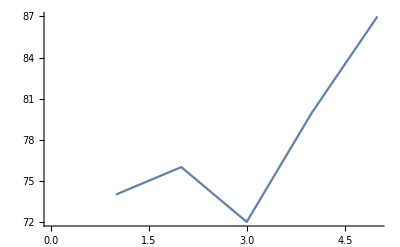

```mathematica
ListLinePlot[{74,76,72,80,87}]
```

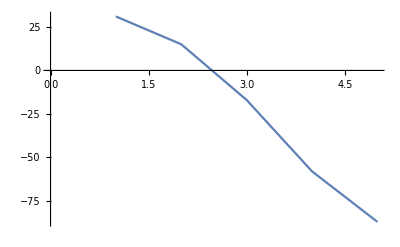

```mathematica
ListLinePlot[{31,15,-17,-17-41,-17-41-29}]
```

```mathematica
aaaa==Import[files[[20]],"String"];
```

```mathematica
aaaa[[1]]
```

Part::partd: Part specification aaaa⟦1⟧ is longer than depth of object.

aaaa⟦1⟧

### Cut 3

```mathematica
Map[Cutter3,files]
```

AbsoluteTime::str: String {305207000, "2017-01-01T00:15:39", 23.66373, -82.24353, 16., 88.9, 91., "", "", "", "", "under way using engine", "", "", "", ""} cannot be interpreted as a date in format Automatic.

AbsoluteTime::str: String {212482000, "2017-01-01T00:03:13", 23.69274, -81.3509, 11.8, 107.5, 112., "", "", "", "", "under way using engine", "", "", 14.5, ""} cannot be interpreted as a date in format Automatic.

AbsoluteTime::str: String {240538000, "2017-01-01T00:03:33", 23.92925, -81.06272, 11.5, -171.6, 238., "", "", "", "", "under way using engine", "", "", "", ""} cannot be interpreted as a date in format Automatic.

General::stop: Further output of AbsoluteTime::str will be suppressed during this calculation.

$Aborted

```mathematica
Cutter3[x_]:=Export[x,Select[SplitBy[SortBy[Import[x],SpaceTimeCode2],SpaceTimeCode2],UniqueVessels[#]≥2&]]
```

```mathematica
files[[1]]
```

/Users/robertmendelsohn/Desktop/Fathom5/xaa.csv

```mathematica
UnitConvert[Quantity[1.9*3/(7*4),"Millimeters"],"Inches"]
```

0.00801462 in

```mathematica
Export["/Users/robertmendelsohn/Desktop/Fathom5/overtaking.txt",overtaking]
```

/Users/robertmendelsohn/Desktop/Fathom5/overtaking.txt

```mathematica
Export["/Users/robertmendelsohn/Desktop/Fathom5/meeting.txt",meeting]
```

/Users/robertmendelsohn/Desktop/Fathom5/meeting.txt

```mathematica
Export["/Users/robertmendelsohn/Desktop/Fathom5/crossing.txt",crossing]
```

/Users/robertmendelsohn/Desktop/Fathom5/crossing.txt